Equation of Motion

```mathematica
EOM={D[((1/2 l^2) θ'[t]^2+((((a l) ω) Sin[ω t]) Sin[θ[t]]) θ'[t]+((1/2 a^2) ω^2) Sin[ω t]^2+g (l Cos[θ[t]]+a Cos[ω t])), θ[t]]-D[D[((1/2 l^2) θ'[t]^2+((((a l) ω) Sin[ω t]) Sin[θ[t]]) θ'[t]+((1/2 a^2) ω^2) Sin[ω t]^2+g (l Cos[θ[t]]+a Cos[ω t])), θ'[t]], t]==0,θ[0]==θo,θ'[0]==V}
```

```mathematica
{-g l Sin[θ[t]]-a l ω^2 Cos[t ω] Sin[θ[t]]-l^2 θ''[t]==0,θ[0]==θo,θ'[0]==V};
sol=DSolve[-g l Sin[θ[t]]-a l ω^2 Cos[t ω] Sin[θ[t]]-l^2 θ''[t]==0,θ[t],t]
```

DSolve[-g l Sin[θ[t]]-a l ω^2 Cos[t ω] Sin[θ[t]]-l^2 θ''[t]==0,θ[t],t]

Lagrangian and Stability

```mathematica
ClearAll[θ,a,l,ω,t]
```

```mathematica
L[θ[t],θ'[t]]=(1/2 l^2) θ'[t]^2+((((a l) ω) Sin[ω t]) Sin[θ[t]]) θ'[t]+((1/2 a^2) ω^2) Sin[ω t]^2+g(l Cos[θ[t]]+a Cos[ω t]);
solve[D[L[θ[t],θ'[t]], θ[t]]-D[D[L[θ[t],θ'[t]], θ'[t]], t]==0,θ''[t]]//Simplify
```

solve[l ((g+a ω^2 Cos[t ω]) Sin[θ[t]]+l θ''[t])==0,θ''[t]]

Effective Potential(U_eff)

Take θ[t] to be made up of two motions: a rapid oscillation with small amplitude (ξ[t]) and a smooth slow oscillation (ϕ[t])

```mathematica
Out[48]/.θ[t]->ξ[t]+ϕ[t]//TrigExpand;
```

```mathematica
ξ''[t]+ϕ''[t]==-(g Cos[ϕ[t]] Sin[ξ[t]])/l-(a ω^2 Cos[t ω] Cos[ϕ[t]] Sin[ξ[t]])/l-(g Cos[ξ[t]] Sin[ϕ[t]])/l-(a ω^2 Cos[t ω] Cos[ξ[t]] Sin[ϕ[t]])/l;
```

```mathematica
Series[%,{ξ[t],0,1}]
```

ξ''[t]+ϕ''[t]==(-g Sin[ϕ[t]]-a ω^2 Cos[t ω] Sin[ϕ[t]])/l+((-g Cos[ϕ[t]]-a ω^2 Cos[t ω] Cos[ϕ[t]]) ξ[t])/l+O[ξ[t]]^2

Keep the leading order term

```mathematica
ξ''[t]==-(a ω^2 Cos[ω t] Sin[ϕ])/l;
```

```mathematica
ϕ''(t)=(a ω^2 Cos[tω](g+a ω^2 Cos[tω])Cos[ϕ[t]]Sin[ϕ])/l^2-Sin[ϕ[t]] Subscript[ω, o]
```

Note that over a period of the rapid oscillation ϕ[t] ~ constant

```mathematica
DSolve[x''[t]==-a/l  ω^2 Cos[t ω] Sin[ϕ],x[t],t]
```

```mathematica
{{x[t]->C[1]+t C[2]+(a Cos[t ω] Sin[ϕ])/l}}
ξ(t)=(a sin(ϕ) cos(ω t))/l
ϕ''(t)=(a ω^2 cos(ω t)(g+a ω^2 cos(ω t))cos(ϕ(t))Sin(ϕ(t)))/l^2-Sin(ϕ(t))Subscript[ω, o]
```

So after averaging the smooth part ϕ[t] we get:

```mathematica
ϕ''(t)=-(a^2 ω^2 sin(ϕ(t)) cos(ϕ(t)))/(2 l^2)-Subscript[ω, o] sin(ϕ(t));
```

Which is equivalent to:

```mathematica
F[t]=-D[(-g/l Cos[ϕ[t]]+a^2 ω^2/(4 l^2) Sin[ϕ[t]]^2), ϕ[t]];
F[t]==ϕ''[t]
```

True

Thus the effective potential U_eff is:

```mathematica
f=D[Subscript[U, eff], ϕ];
CriticalPoints=Solve[f==0,ϕ];
FullSimplify[CriticalPoints, C[1]==0]
```

{{ϕ→0},{ϕ→π},{ϕ→ArcTan[-(2 l^2 ω_o^2)/(a^2 ω^2),-(√(a^4 ω^4-4 l^4 ω_o^4))/(a^2 ω^2)]},{ϕ→ArcTan[-(2 l^2 ω_o^2)/(a^2 ω^2),(√(a^4 ω^4-4 l^4 ω_o^4))/(a^2 ω^2)]}}

This is equivalent to:

```mathematica
Sol={{ϕ->0},{ϕ->π},{ϕ->ArcCos[-(2 Subscript[ω, o]^2 l^2)/(a^2 ω^2)]},{ϕ->2π-ArcCos[-(2 Subscript[ω, o]^2 l^2)/(a^2 ω^2)]}};
Cond=D[f, ϕ]/.Sol
```

{(a^2 ω^2)/(2 l^2)+ω_o^2,(a^2 ω^2)/(2 l^2)-ω_o^2,-(a^2 ω^2 (1-(4 l^4 ω_o^4)/(a^4 ω^4)))/(2 l^2),-(a^2 ω^2 (1-(4 l^4 ω_o^4)/(a^4 ω^4)))/(2 l^2)}

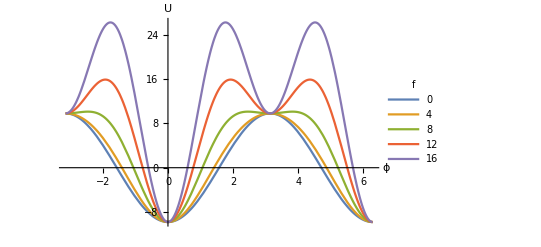

```mathematica
Subscript[U, eff][ϕ_,l_,a_,ω_]:=-9.8/l Cos[ϕ]+a^2 ω^2/(4 l^2) Sin[ϕ]^2;
Plot[Evaluate@Table[Subscript[U, eff][ϕ,1,0.1,2π f],{f,0,16 ,4}],{ϕ,-π,2π},PlotLegends->LineLegend[Table[f,{f,0,16 ,4}],LegendLabel->f],AxesLabel->{ϕ,U}]
```

Big thank you to Atef Sheekhon and John Niman (2022)